```mathematica
NP=179;
funtest=Import["/Users/probert/ETH/rph_dyn/cl2o2/eigfun.dat", "List"];
potential=Import["/Users/probert/ETH/rph_dyn/cl2o2/fort.7", "Table"];
energies=Import["/Users/probert/ETH/rph_dyn/cl2o2/fort.4", "List"];
wp = Import["/Users/probert/ETH/rph_dyn/cl2o2/DM/test/wavepacketdm.out", "Table"];
NT=61;
DX=360/NP;
DT=0.1;
INTERPOL=2;
l=0;
wavepacket = Table[{wp[[i,2]],wp[[i,1]],wp[[i,3]]},{i,1,NP*NT}];
wpi=Table[{0,0,0},{i,1,NT*NP*INTERPOL}];
wpi2=Table[{0,0,0},{i,1,NT*NP}];
frame=Table[{0,0,0},{i,1,NT*NP*INTERPOL}];
Do[
   Do[ 
     l=l+1; 
     frame[[l]] = {DX*(k-0.5)/INTERPOL,DT*(j-1),0};
     wpi[[l]] = {DX*(k-0.5)/INTERPOL,DT*(j-1),Interpolation[wp[[(j-1)*NP+1;;j*NP,3]]][1+(k-1)/INTERPOL]}
     ,{k,1,INTERPOL*(NP-1)+1}]
    ,{j,1,NT,1}]
l=0;
Do[
   Do[ 
     l=l+1; 
     wpi2[[l]] = {DX*(k-0.5),DT*(j-1),wp[[(j-1)*NP+k,3]]}
     ,{k,1,NP,1}]
    ,{j,1,NT,2}]

(*wavepacket = Table[ {wp[[i,2]],wp[[i,1]],wp[[i,3]]},{i,1,NP*NT}];*)
```

```mathematica
(*tf=250.
Do[
If[wpi[[j,2]]>tf,wpi[[j,3]]=-1];
,{j,1,NT*NP*INTERPOL}];*)
(*Draw Potential *)
maxz=Max[wpi[[1;;NT*NP,3]]]
maxp=Max[potential[[1;;NP,2]]]
minp=Min[potential[[1;;NP,2]]]
(*pot=Interpolation[(potential)];
Plot[pot[x],{x,10,340}]
lastp=Plot3D[(pot[x]-minp)/maxp*maxz,{x,40,310},{t,8,tf+5*DT},PlotRange->{{40,310},{8,tf+6*DT},{0.0001,0.18}},
ImageSize->750,BoxRatios->{1.75,1.1,0.35},Boxed->False,Axes->{False,True,False},Ticks->None]*)
(*potplot = Table[{potential[[k,1]],tf+5*DT,(potential[[k,2]]-Min[potential[[1;;NP,2]]])/Max[potential[[1;;NP]]]*maxz},{k,1,NP}];
last=ListPointPlot3D[potplot,PlotRange->{{30,330},{2,tf+5*DT},{-0.0002,0.15}},Ticks->{None,None,{0,0.1,0.15}},ViewPoint->{3,-4.8,3}
,ImageSize->750,BoxRatios->{1.75,1.1,0.35},Boxed->True,Axes->{True,True,True},AxesEdge->{{1,-1},None,{-1,1}}]
pot2D=ListLinePlot[Table[{potential[[k,1]],(potential[[k,2]]-Min[potential[[1;;NP,2]]])/Max[potential[[100]]]*maxz},{k,1,NP}],Frame->True,
PlotRange->{{30,330},All}];
pot3D=Graphics3D[pot2D[[1]]/.{x_Real,y_Real}->{x,tf+5*DT,y},ImageSize->750,BoxRatios->{1.75,1.1,0.35}
,ViewPoint->{3,-4.8,3},Axes->True,PlotRange->{{30,330},{0,tf+5*DT},All},Axes->{True,True,True},Boxed->False,
AxesEdge->{{1,-1},None,{-1,1}},Ticks->{None,None,Automatic}]*)
part1=ListPlot3D[wpi,
Mesh->{29,31},MeshStyle->{Thickness[0.001],Thickness[0.001]},
PlotRange->{{40,320},All,{-0.0002,0.18}},PerformanceGoal->Quality,ImageSize->750,BoxRatios->{1.75,1.1,0.35}
,Boxed->False,AxesEdge->{{0,0},{1,0},{0,0}},ViewPoint->{3,-4.8,3},
(*PlotStyle->Directive[(*Glow[White],*)Specularity[White,12]],*)LabelStyle->Directive[FontFamily->"Times",FontSize->20],ClippingStyle->None]
(*Show[part1,pot3D]*)
(*part2=ListPlot3D[wpi,AxesLabel->{"τ/°","t/μs","|Ψ|^2"}, 
Mesh->{61,31},MeshStyle->{Thickness[0.001],Thickness[0.001]},
PlotRange->{{220,320},All,All},PerformanceGoal->Quality,ImageSize->500,BoxRatios->{0.5,1,0.2},Boxed->False,Axes->False]*)
```

0.152925

4040.72

1441.17

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(*GraphicsRow[{part1,part2},ImageSize->1000,Spacings->0.]*)
spaceing={40,140,220,320};
offset=10
wps=Table[0,{t,1,NT}];
kx=(NP-0.5)*INTERPOL
Do[
wps[[t]]=Join[Table[wpi[[(t-1)*kx+i]],{i,spaceing[[1]],spaceing[[2]]}],Table[wpi[[(t-1)*kx+i]]-{spaceing[[3]]-spaceing[[2]]-offset,0,0},{i,spaceing[[3]],spaceing[[4]]}]],{t,1,NT}]
(*GraphicsRow[{part1,part2}]*)
wps//Flatten;
wps2=Partition[%,3];
ListPlot3D[wps2,AxesLabel->{"τ/°","t/ns"," |Ψ|^2"}, 
Mesh->{31,31},MeshStyle->{Thickness[0.001],Thickness[0.001]},
PlotRange->{{spaceing[[1]],250},All,{-0.01,0.15}},PerformanceGoal->Quality,ImageSize->500,BoxRatios->{0.75,1.1,0.25},RegionFunction->Function[{x,y,z},x<spaceing[[2]]||x>(spaceing[[2]]+offset+1)],(*BoundaryStyle->Thick,*)Ticks->{{{spaceing[[1]],spaceing[[1]]},{spaceing[[2]],spaceing[[2]]},{spaceing[[2]]+offset,spaceing[[3]]},{spaceing[[4]]-(spaceing[[3]]-spaceing[[2]]-offset),spaceing[[4]]}},Automatic,Automatic},PlotStyle->Directive[(*Glow[White],*)Specularity[White,12]]]
(*ListPlot3D[wpi,AxesLabel->{"τ/°","t/ms","|Ψ|^2"},
Mesh->{61,31},MeshStyle->{Thickness[0.001],Thickness[0.001]},
PlotRange->{All,All,All},PerformanceGoal->Quality,ImageSize->500]*)
```

10

357.

-Graphics3D-

-Graphics3D-

```mathematica
2
```

0.162

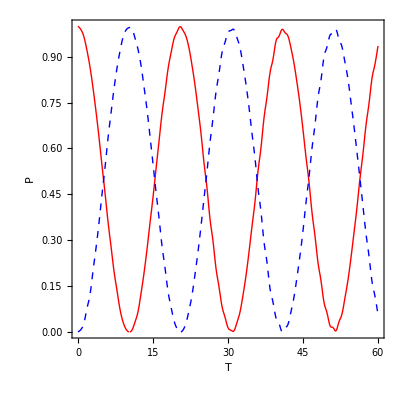

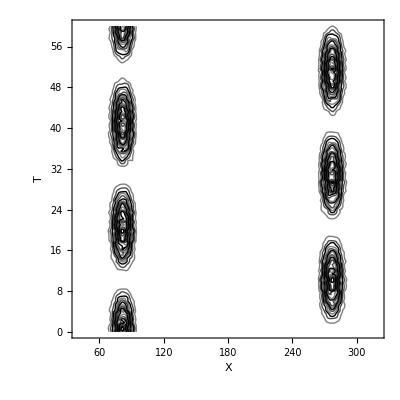

```mathematica
maxz=Max[wpi[[1;;NT*NP,3]]]
(*determine how much of the probability is ins left/right half of potential *)
pL=Table[{DT*(t-1),Sum[wp[[(t-1)*NP+j,3]],{j,1,0.5*(NP+1)}]},{t,1,NT}];
pR=Table[{DT*(t-1),Sum[wp[[(t-1)*NP+j,3]],{j,0.5*(NP-1),NP}]},{t,1,NT}];
ListLinePlot[{pL,pR},Frame->True,FrameLabel->{"T","P"},
PlotRange->{{0,60},{0,1}},PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick]},
AspectRatio->1,InterpolationOrder->2,LabelStyle->Directive[FontFamily->"Times",FontSize->20]]
(*_-_-_-_*)
ListContourPlot[wpi,ColorFunctionScaling->True,ColorFunction->"TemperatureMap",ContourShading->None
,PlotRange->{{40,320},{0,60},{0.002,maxz}},FrameLabel->{"X","T"},ContourStyle->{Opacity[0.5],Opacity[0.7],Black},
Contours->15,LabelStyle->Directive[FontFamily->"Times",FontSize->20]]
```

{{0.,1.},{0.6,0.880338},{1.2,0.665257},{1.8,0.286377},{2.4,-0.076714},{3.,-0.439416},{3.6,-0.665584},{4.2,-0.769857},{4.8,-0.716463},{5.4,-0.546798},{6.,-0.314724},{6.6,-0.067147},{7.2,0.118984},{7.8,0.234657},{8.4,0.243348},{9.,0.191576},{9.6,0.09074},{10.2,0.014773},{10.8,-0.025973},{11.4,0.024469},{12.,0.119961},{12.6,0.284377},{13.2,0.405827},{13.8,0.511936},{14.4,0.469123},{15.,0.361488},{15.6,0.088937},{16.2,-0.194572},{16.8,-0.538389},{17.4,-0.770243},{18.,-0.918063},{18.6,-0.874961},{19.2,-0.684974},{19.8,-0.357187},{20.4,0.048359},{21.,0.429679},{21.6,0.754955},{22.2,0.905642},{22.8,0.925481},{23.4,0.745775},{24.,0.486804},{24.6,0.136035},{25.2,-0.163974},{25.8,-0.418099},{26.4,-0.527944},{27.,-0.542311},{27.6,-0.42901},{28.2,-0.287313},{28.8,-0.111605},{29.4,-0.011908},{30.,0.052876},{30.6,0.005625},{31.2,-0.052985},{31.8,-0.160843},{32.4,-0.197571},{33.,-0.191709},{33.6,-0.074535},{34.2,0.109693},{34.8,0.336347},{35.4,0.56283},{36.,0.693117},{36.6,0.739093},{37.2,0.595888},{37.8,0.368939},{38.4,-0.009162},{39.,-0.359708},{39.6,-0.719613},{40.2,-0.912531},{40.8,-0.989176},{41.4,-0.851452},{42.,-0.594414},{42.6,-0.214952},{43.2,0.166241},{43.8,0.510476},{44.4,0.724855},{45.,0.803869},{45.6,0.720752},{46.2,0.535365},{46.8,0.274424},{47.4,0.027945},{48.,-0.173613},{48.6,-0.278056},{49.2,-0.286998},{49.8,-0.227171},{50.4,-0.11561},{51.,-0.042162},{51.6,0.01699},{52.2,-0.041953},{52.8,-0.112827},{53.4,-0.280772},{54.,-0.376023},{54.6,-0.474917},{55.2,-0.41557},{55.8,-0.295571},{56.4,-0.029218},{57.,0.259964},{57.6,0.570999},{58.2,0.795278},{58.8,0.896542},{59.4,0.838211},{60.,0.612516}}

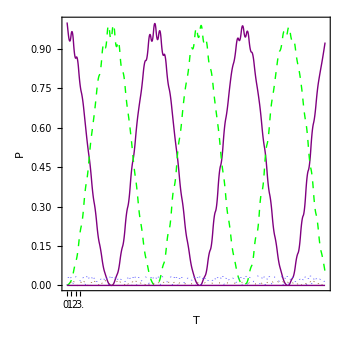

41

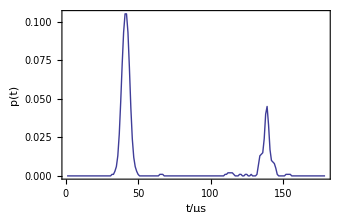

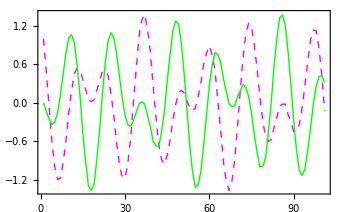

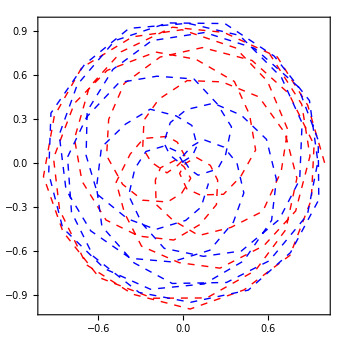

```mathematica
statepop=Import["/Users/probert/ETH/rph_dyn/cl2o2/1188.08/survprob_60mus_RA.out", "Table"];
time=statepop[[1;;NT,1]]*10^6;
survprob=statepop[[1;;NT,2]];
NE=60;
Do[
p[i]=Table[{time[[j]],statepop[[j,i+2]]},{j,1,NT}],
{i,1,90}]
p[1]
ListPlot[{p[3],p[6],p[69],p[72],Table[{time[[i]],p[57][[i,2]]+p[60][[i,2]]},{i,1NT}]},PlotRange->{{0,60},{0,1}},InterpolationOrder->2,PlotStyle->{Directive[Purple,Thick],Directive[Green,Dashed,Thick],Directive[Brown,Dotted,Thick],Directive[Lighter[Blue],Dotted,Thick]},Ticks->{{0.,1.,2.,3.},Automatic},Frame->True,FrameLabel->{"T","P"},Axes->{False,True},Joined->True,AspectRatio->1,LabelStyle->Directive[FontFamily->"Times",FontSize->20]]
(*Show[%,ListPlot[{p[3],p[6],p[69],p[72]},PlotRange->{All,{0,1}},InterpolationOrder->2,PlotStyle->{Red,Blue,Magenta,Cyan},PlotMarkers->Automatic]]*)
t=41
ListLinePlot[wp[[((t-1)*NP+1);;t*NP,3]],PlotRange->{All,All},Frame->True,FrameLabel->{"t/μs","p(t)"}]
ListLinePlot[{p[1][[1;;NT,2]]-p[2][[1;;NT,2]],p[4][[1;;NT,2]]-p[5][[1;;NT,2]]},PlotStyle->{Directive[Magenta,Dashed,Thick],Directive[Green,Thick]},PlotRange->{All,All},Frame->True,Axes->False]
complot=Table[{p[1][[i,2]],p[2][[i,2]]},{i,1,NT}];
complot2=Table[{p[4][[i,2]],p[5][[i,2]]},{i,1,NT}];
ListPlot[{complot,complot2},Joined->True,PlotStyle->{Directive[Red,Dashed,Thick],Directive[Blue,Thick]},PlotRange->{All,All},Frame->True,AspectRatio->1]
```

```mathematica
!
```

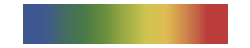
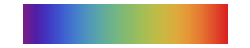
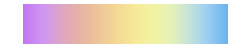
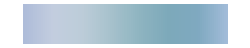
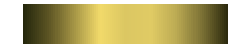
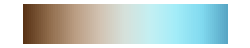
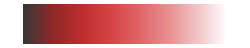
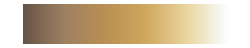

DarkRainbow | Rainbow | Pastel
Aquamarine | BrassTones | BrownCyanTones
CherryTones | CoffeeTones | FuchsiaTones
GrayTones | GrayYellowTones | GreenPinkTones
PigeonTones | RedBlueTones | RustTones
SiennaTones | ValentineTones | AlpineColors
ArmyColors | AtlanticColors | AuroraColors
AvocadoColors | BeachColors | CandyColors
CMYKColors | DeepSeaColors | FallColors
FruitPunchColors | IslandColors | LakeColors
MintColors | NeonColors | PearlColors
PlumColors | RoseColors | SolarColors
SouthwestColors | StarryNightColors | SunsetColors
ThermometerColors | WatermelonColors | RedGreenSplit
DarkTerrain | GreenBrownTerrain | LightTerrain
SandyTerrain | BlueGreenYellow | LightTemperatureMap
TemperatureMap | BrightBands | DarkBands

{{39.7207,0,0.},{40.7263,0,0.},{41.7318,0,0.},{42.7374,0,0.},{43.743,0,0.},{44.7486,0,0.},{45.7542,0,0.},{46.7598,0,0.},{47.7654,0,0.},{48.7709,0,0.},{49.7765,0,0.},{50.7821,0,0.},{51.7877,0,0.},{52.7933,0,0.},{53.7989,0,0.},{54.8045,0,0.},{55.8101,0,0.},{56.8156,0,0.},{57.8212,0,0.},{58.8268,0,0.},{59.8324,0,0.},{60.838,0,0.},{61.8436,0,-0.0000625},{62.8492,0,0.},{63.8547,0,0.0003125},{64.8603,0,0.001},{65.8659,0,0.00225},{66.8715,0,0.004},{67.8771,0,0.0060625},{68.8827,0,0.009},{69.8883,0,0.013125},{70.8939,0,0.019},{71.8994,0,0.0274375},{72.905,0,0.038},{73.9106,0,0.050625},{74.9162,0,0.065},{75.9218,0,0.08125},{76.9274,0,0.098},{77.933,0,0.114438},{78.9385,0,0.129},{79.9441,0,0.14},{80.9497,0,0.147},{81.9553,0,0.148875},{82.9609,0,0.146},{83.9665,0,0.137938},{84.9721,0,0.126},{85.9777,0,0.110813},{86.9832,0,0.094},{87.9888,0,0.077125},{88.9944,0,0.061},{90.,0,0.0470625},{91.0056,0,0.035},{92.0112,0,0.025},{93.0168,0,0.017},{94.0223,0,0.011125},{95.0279,0,0.007},{96.0335,0,0.0045},{97.0391,0,0.003},{98.0447,0,0.0018125},{99.0503,0,0.001},{100.056,0,0.000375},{101.061,0,0.},{102.067,0,-0.0000625},{103.073,0,0.},{104.078,0,0.},{105.084,0,0.},{106.089,0,0.},{107.095,0,0.},{108.101,0,0.},{109.106,0,0.},{110.112,0,0.},{111.117,0,0.},{112.123,0,0.},{113.128,0,0.},{114.134,0,0.},{115.14,0,0.},{116.145,0,0.},{117.151,0,0.},{118.156,0,0.},{119.162,0,0.},{120.168,0,0.},{110.838,0,0.},{111.844,0,0.},{112.849,0,0.},{113.855,0,0.},{114.86,0,0.},{115.866,0,0.},{116.872,0,0.},{117.877,0,0.},{118.883,0,0.},{119.888,0,0.},{120.894,0,0.},{121.899,0,0.},{122.905,0,0.},{123.911,0,0.},{124.916,0,0.},{125.922,0,0.},{126.927,0,0.},{127.933,0,0.},{128.939,0,0.},{129.944,0,0.},{130.95,0,0.},{131.955,0,0.},{132.961,0,0.},{133.966,0,0.},{134.972,0,0.},{135.978,0,0.},{136.983,0,0.},{137.989,0,0.},{138.994,0,0.},{140.,0,0.},{141.006,0,0.},{142.011,0,0.},{143.017,0,0.},{144.022,0,0.},{145.028,0,0.},{146.034,0,0.},{147.039,0,0.},{148.045,0,0.},{149.05,0,0.},«16122»,{81.9553,116.,0.073},{82.9609,116.,0.072},{83.9665,116.,0.0689375},{84.9721,116.,0.064},{85.9777,116.,0.057125},{86.9832,116.,0.049},{87.9888,116.,0.04},{88.9944,116.,0.031},{90.,116.,0.022875},{91.0056,116.,0.016},{92.0112,116.,0.0113125},{93.0168,116.,0.008},{94.0223,116.,0.005625},{95.0279,116.,0.004},{96.0335,116.,0.0028125},{97.0391,116.,0.002},{98.0447,116.,0.0014375},{99.0503,116.,0.001},{100.056,116.,0.0004375},{101.061,116.,0.},{102.067,116.,-0.0000625},{103.073,116.,0.},{104.078,116.,0.},{105.084,116.,0.},{106.089,116.,0.},{107.095,116.,0.},{108.101,116.,0.},{109.106,116.,0.},{110.112,116.,0.},{111.117,116.,0.},{112.123,116.,0.},{113.128,116.,0.},{114.134,116.,0.},{115.14,116.,0.},{116.145,116.,0.},{117.151,116.,0.},{118.156,116.,0.},{119.162,116.,0.},{120.168,116.,0.},{110.838,116.,0.},{111.844,116.,0.},{112.849,116.,0.},{113.855,116.,0.},{114.86,116.,0.},{115.866,116.,0.},{116.872,116.,0.},{117.877,116.,0.},{118.883,116.,0.},{119.888,116.,0.},{120.894,116.,0.},{121.899,116.,0.},{122.905,116.,0.},{123.911,116.,0.},{124.916,116.,0.},{125.922,116.,0.},{126.927,116.,0.},{127.933,116.,0.},{128.939,116.,-0.0000625},{129.944,116.,0.},{130.95,116.,0.0003125},{131.955,116.,0.001},{132.961,116.,0.00225},{133.966,116.,0.004},{134.972,116.,0.006125},{135.978,116.,0.009},{136.983,116.,0.0130625},{137.989,116.,0.018},{138.994,116.,0.0235625},{140.,116.,0.03},{141.006,116.,0.03775},{142.011,116.,0.046},{143.017,116.,0.05425},{144.022,116.,0.062},{145.028,116.,0.0689375},{146.034,116.,0.074},{147.039,116.,0.0759375},{148.045,116.,0.075},{149.05,116.,0.0705625},{150.056,116.,0.064},{151.061,116.,0.056375},{152.067,116.,0.048},{153.073,116.,0.03925},{154.078,116.,0.031},{155.084,116.,0.0245},{156.089,116.,0.019},{157.095,116.,0.0140625},{158.101,116.,0.01},{159.106,116.,0.007125},{160.112,116.,0.005},{161.117,116.,0.00325},{162.123,116.,0.002},{163.128,116.,0.001375},{164.134,116.,0.001},{165.14,116.,0.0004375},{166.145,116.,0.},{167.151,116.,-0.0000625},{168.156,116.,0.},{169.162,116.,0.},{170.168,116.,0.},{171.173,116.,0.},{172.179,116.,0.},{173.184,116.,0.},{174.19,116.,0.},{175.196,116.,0.},{176.201,116.,0.},{177.207,116.,0.},{178.212,116.,0.},{179.218,116.,0.},{180.223,116.,0.},{181.229,116.,0.},{182.235,116.,0.},{183.24,116.,0.},{184.246,116.,0.},{185.251,116.,0.},{186.257,116.,0.},{187.263,116.,0.},{188.268,116.,0.},{189.274,116.,0.},{190.279,116.,0.},{191.285,116.,0.}}

```mathematica
GraphicsGrid[Partition[ColorData[#,"Image"]&/@ColorData["Gradients"],3],ImageSize->300]
Table[ColorData["Gradients"][[i+1;;i+3]],{i,0,48,3}]//TableForm
```